## Data

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import ["task2.csv"];
claassMinus1=data[[Flatten@Position[data[[All,3]],-1]]];
claassMinus2=data[[Flatten@Position[data[[All,3]],1]]];
```

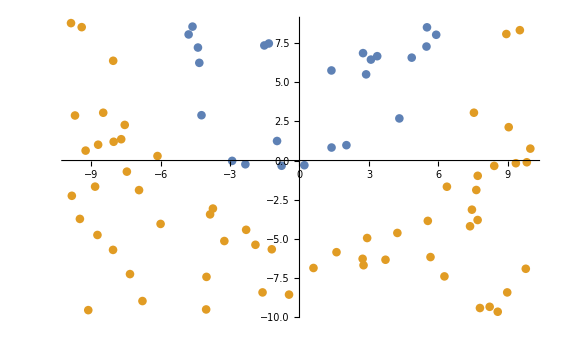

```mathematica
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]]}]
```

## Poly Kernel

```mathematica
n=Length@data;
alpha=Array[α,n];
X=data⟦All,;;2⟧;
Y=data⟦All,3⟧;
```

```mathematica
φ[x_]:={x⟦1⟧^2,x⟦2⟧^2,√2*x⟦1⟧*x⟦2⟧}
```

```mathematica
K[x_,z_]:=(x.z)^2
```

```mathematica
K[X[[1]],X[[2]]]
```

7758.29

```mathematica
φ[X[[1]]].φ[X[[2]]]
```

7758.29

```mathematica
L=Total[alpha]-1/2*Sum[alpha⟦i⟧*alpha⟦j⟧*Y⟦i⟧*Y⟦j⟧*K[X⟦i⟧,X⟦j⟧],{i,1,n},{j,1,n}];
```

```mathematica
condition=Total[alpha*Y];
```

```mathematica
res=NMaximize[{L,Table[alpha[[i]]≥0,{i,1,n}],condition==0},alpha]
```

$Aborted

```mathematica
Flatten@{Table[alpha[[i]]≥0,{i,1,n}],condition==0}
```

{α[1]≥0,α[2]≥0,α[3]≥0,α[4]≥0,α[5]≥0,α[6]≥0,α[7]≥0,α[8]≥0,α[9]≥0,α[10]≥0,α[11]≥0,α[12]≥0,α[13]≥0,α[14]≥0,α[15]≥0,α[16]≥0,α[17]≥0,α[18]≥0,α[19]≥0,α[20]≥0,α[21]≥0,α[22]≥0,α[23]≥0,α[24]≥0,α[25]≥0,α[26]≥0,α[27]≥0,α[28]≥0,α[29]≥0,α[30]≥0,α[31]≥0,α[32]≥0,α[33]≥0,α[34]≥0,α[35]≥0,α[36]≥0,α[37]≥0,α[38]≥0,α[39]≥0,α[40]≥0,α[41]≥0,α[42]≥0,α[43]≥0,α[44]≥0,α[45]≥0,α[46]≥0,α[47]≥0,α[48]≥0,α[49]≥0,α[50]≥0,α[51]≥0,α[52]≥0,α[53]≥0,α[54]≥0,α[55]≥0,α[56]≥0,α[57]≥0,α[58]≥0,α[59]≥0,α[60]≥0,α[61]≥0,α[62]≥0,α[63]≥0,α[64]≥0,α[65]≥0,α[66]≥0,α[67]≥0,α[68]≥0,α[69]≥0,α[70]≥0,α[71]≥0,α[72]≥0,α[73]≥0,α[74]≥0,α[75]≥0,α[76]≥0,α[77]≥0,α[78]≥0,α[79]≥0,α[80]≥0,α[81]≥0,α[82]≥0,α[83]≥0,α[84]≥0,α[85]≥0,α[1]+α[2]-α[3]+α[4]+α[5]+α[6]+α[7]+α[8]+α[9]-α[10]+α[11]+α[12]-α[13]+α[14]+α[15]+α[16]+α[17]+α[18]-α[19]+α[20]-α[21]+α[22]+α[23]+α[24]+α[25]-α[26]+α[27]+α[28]-α[29]+α[30]+α[31]+α[32]+α[33]-α[34]+α[35]+α[36]-α[37]+α[38]+α[39]-α[40]+α[41]+α[42]+α[43]+α[44]+α[45]+α[46]+α[47]-α[48]-α[49]+α[50]-α[51]-α[52]+α[53]+α[54]-α[55]+α[56]+α[57]+α[58]+α[59]+α[60]+α[61]+α[62]+α[63]-α[64]-α[65]+α[66]+α[67]+α[68]-α[69]-α[70]+α[71]+α[72]-α[73]+α[74]-α[75]-α[76]-α[77]+α[78]+α[79]+α[80]+α[81]+α[82]-α[83]+α[84]+α[85]==0}

```mathematica
res2=QuadraticOptimization[-L,Flatten@{Table[alpha[[i]]≥0,{i,1,n}],condition==0},alpha]
```

QuadraticOptimization::noprog: Lack of progress.

{α[1]→107901.,α[2]→126843.,α[3]→814831.,α[4]→283942.,α[5]→4.61994×10^6,α[6]→121455.,α[7]→462276.,α[8]→188572.,α[9]→7.29831×10^6,α[10]→685716.,α[11]→148087.,α[12]→190241.,α[13]→954266.,α[14]→1.02797×10^6,α[15]→141682.,α[16]→264125.,α[17]→761364.,α[18]→349826.,α[19]→807597.,α[20]→1.19993×10^6,α[21]→779248.,α[22]→474995.,α[23]→716907.,α[24]→1.35008×10^6,α[25]→2.1175×10^6,α[26]→800424.,α[27]→364449.,α[28]→108580.,α[29]→1.42388×10^6,α[30]→396639.,α[31]→196181.,α[32]→87371.6,α[33]→775932.,α[34]→1.81895×10^6,α[35]→79800.8,α[36]→112201.,α[37]→1.58465×10^6,α[38]→267388.,α[39]→682082.,α[40]→884515.,α[41]→366751.,α[42]→232256.,α[43]→241440.,α[44]→3.99156×10^6,α[45]→145101.,α[46]→2.07669×10^6,α[47]→309344.,α[48]→1.62401×10^6,α[49]→738101.,α[50]→114737.,α[51]→1.01855×10^6,α[52]→3.7753×10^6,α[53]→220118.,α[54]→161311.,α[55]→1.11612×10^6,α[56]→94172.7,α[57]→1.16653×10^6,α[58]→223710.,α[59]→928221.,α[60]→127835.,α[61]→97211.9,α[62]→1.14008×10^6,α[63]→513849.,α[64]→1.22728×10^6,α[65]→1.04533×10^6,α[66]→143853.,α[67]→101154.,α[68]→247428.,α[69]→3.60616×10^6,α[70]→814449.,α[71]→1.38205×10^6,α[72]→85456.7,α[73]→3.54281×10^6,α[74]→180100.,α[75]→2.54786×10^6,α[76]→3.93945×10^6,α[77]→4.8867×10^6,α[78]→431993.,α[79]→516662.,α[80]→260168.,α[81]→167147.,α[82]→276015.,α[83]→868421.,α[84]→141198.,α[85]→197934.}

```mathematica
resAlpha=res2[[All,2]]
```

{107901.,126843.,814831.,283942.,4.61994×10^6,121455.,462276.,188572.,7.29831×10^6,685716.,148087.,190241.,954266.,1.02797×10^6,141682.,264125.,761364.,349826.,807597.,1.19993×10^6,779248.,474995.,716907.,1.35008×10^6,2.1175×10^6,800424.,364449.,108580.,1.42388×10^6,396639.,196181.,87371.6,775932.,1.81895×10^6,79800.8,112201.,1.58465×10^6,267388.,682082.,884515.,366751.,232256.,241440.,3.99156×10^6,145101.,2.07669×10^6,309344.,1.62401×10^6,738101.,114737.,1.01855×10^6,3.7753×10^6,220118.,161311.,1.11612×10^6,94172.7,1.16653×10^6,223710.,928221.,127835.,97211.9,1.14008×10^6,513849.,1.22728×10^6,1.04533×10^6,143853.,101154.,247428.,3.60616×10^6,814449.,1.38205×10^6,85456.7,3.54281×10^6,180100.,2.54786×10^6,3.93945×10^6,4.8867×10^6,431993.,516662.,260168.,167147.,276015.,868421.,141198.,197934.}

```mathematica
w=Sum[resAlpha[[i]]*Y[[i]]*φ[X[[i]]],{i,1,n}]
```

{0.166015,-0.00366175,-0.00992666}

```mathematica
plos=w.{x1^2,x2^2,√2*x1*x2}
```

0.166015 x1^2-0.0140384 x1 x2-0.00366175 x2^2

```mathematica
fun[resu_,x_]:=resu/.{x1->x}
```

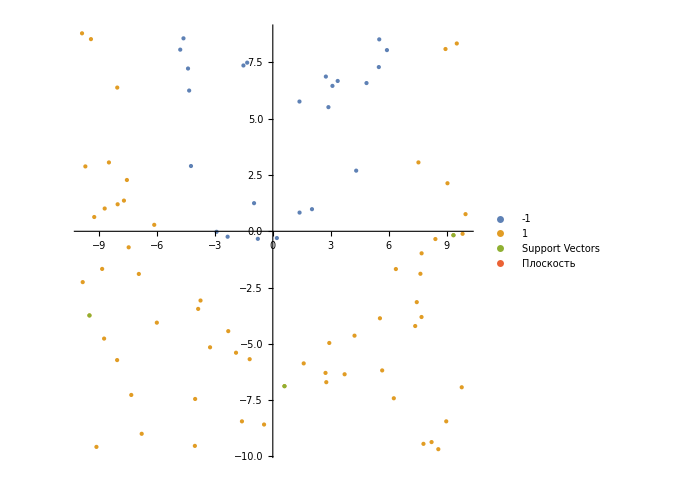

```mathematica
points=Table[{x,fun[resu,x]},{x,-1.5,1.5,0.001}];
ListPlot[{claassMinus1[[All,;;2]],claassMinus2[[All,;;2]],{X[[1]],X[[2]],X[[5]]},points},PlotLegends->{-1,1,"Support Vectors","Плоскость"},PlotStyle->PointSize[Large],Joined->{False,False,False},AspectRatio->1,ImageSize->500]
```